# The Paul Ion Trap

In order to build a quantum computer we need something that can serve as a qubit. It should behave as a quantum mechanical system but be scalable. Several candidates for possible quantum computer applications have been advanced.

Here we consider a scheme in which trapped atomic ions serve as the fundamental qubit.

A working quantum computer should allow individual qubits to be individually addressed, allow two or more qubits to "talk" to each other (in order to built gates), and be scalable. The ion-trap has met these and other three criteria, but before utilizing the ions as qubits on must be able tor trap and control a configuration of ions in an enclosed space. The Paul trap  serves such a purpose and we describe the physics behind the Paul trap below.

The ion is a charged particle and responds to an electric potential  field.  You may remember from freshman physics that the electric potential of a cylinder, held at a constant potential V_0, has the form

V(x,y) = V_0 + λ Log(R/ρ)  for ρ > R
           = V_0  for ρ ⩽ R

where ρ =√(x^2+y^2)  is the distance from the axis along the center of the cylinder, R is the radius of  the cylinder and λ is a constant. Lets make a 3D  plot of this  potential.

```mathematica
(* x,y are the coordinates of the observation point, x0, y0 are the coordinates in which the axis of the cylinder passes through. V0, R are deined above. Choose abitrary values for V0, and R*)

ClearAll["Global`*"];
V0=2;
v[x_,y_,x0_,y0_,R_]:=Which[ Sqrt[(x-x0)^2+(y-y0)^2]>R,V0+Log[R/Sqrt[(x-x0)^2+(y-y0)^2]] ,Sqrt[(x-x0)^2+(y-y0)^2]<=R,V0]
```

```mathematica
(* let the axis of the cylinder pass through the origin *)
Plot3D[v[x,y,0,0,0.5],{x,-10,10},{y,-10,10},PlotPoints->100,PlotRange->All]
```

-Graphics3D-

A positively charged particle in this landscape “runs downhill “, no matter where it is placed therefore, It cannot be utilized as a trap. So let’s include another cylinder with a negative potential to counteract this one. We displace the cylinders so the resulting potential has form shown below. Such a configuration is called a dipole.

```mathematica
dipole[x_,y_]:=v[x,y,0,2,0.5]-v[x,y,0,-2,0.5]
```

```mathematica
Plot3D[dipole[x,y],{x,-10,10},{y,-10,10},PlotPoints->100,PlotRange->All]
```

-Graphics3D-

In this configuration a positive charged particle ``falls ’’ into the potential minimum (i.e. the surface of the negatively charged cylinder), and so this configuration is also an unsatisfactory trap. We try again by doubling the dipoles, so the four cylinders have alternating signs of charge as shown below. This configuration is called a quadrupole.

```mathematica
quadrupole[x_,y_]:=v[x,y,0,2,0.5]-v[x,y,-2,0,0.5]+v[x,y,0,-2,0.5]-v[x,y,2,0,0.5]
```

```mathematica
Plot3D[quadrupole[x,y],{x,-4,4},{y,-4,4},PlotPoints->100,PlotRange->All]
```

-Graphics3D-

It looks like we might have succeeded as a charged particle situated at the origin experiences no force since the potential landscape is flat in that region. A careful analysis shows that near the origin the potential has the form

V(x,y) = V_0 (x^2- y^2) Φ_0/2  where Φ_0 is a constant.

```mathematica
Vquad[x_,y_]=V0(x^2-y^2)
```

2 (x^2-y^2)

```mathematica
Plot3D[Vquad[x,y],{x,-4,4},{y,-4,4}]
```

-Graphics3D-

Unfortunately, the smallest nudge on the positively charged particle located at the origin forces it to ``fall ’’ down the hills and into the negatively charged cylinders. This describes an unstable equilibrium for the ion, and again fails as a suitable trap.  

Now, instead of a constant voltage V_0 on the electrodes, we change the polarity in a time-dependent way. Lets consider
a Cos[ω t] dependence so that the potential near the origin looks like,

V(x,y) = V_0 Cos(ω t) (x^2- y^2) Φ_0/2


-Graphics-

```mathematica
Vquad[x_,y_,t_]=V0 Cos[ω t](x^2-y^2) /. ω->2Pi
```

2 (x^2-y^2) Cos[2 π t]

```mathematica
Manipulate[Plot3D[Vquad[x,y,t],{x,-4,4},{y,-4,4},PlotRange->{-30,30}],{t,0,2},SaveDefinitions->True]
```

So how does a charged particle behave under the influence of such a "rotating saddle" potential ? 
The force that a particle experiences is the negative of the gradient of the potential times its charge q
i.e.
F_x =  -q  x  V_0 Cos(ω t) 
F_y =   q  y  V_0 Cos(ω t) 

and Newton's equation of motion are

m x^(..) =  -q  x  V_0 Cos(ω t) 
m y^(..) =   q  y  V_0 Cos(ω t)

```mathematica
eq1=x''[t]==- q/m  x[t]Cos[ω t]  /.{q->1,m->1,ω->2Pi}
eq2=y''[t]==  q/m  y[t]Cos[ω t]  /.{q->1,m->1,ω->2Pi}

(* initial conditions *)

x0=2.0;
y0=-1.0;
v0x=1.0;
v0y=1.0;
```

x''[t]==-Cos[2 π t] x[t]

y''[t]==Cos[2 π t] y[t]

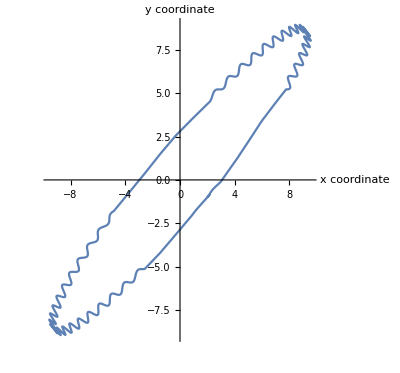

```mathematica
(* we solve for the equations of motion eq1,eq2 given above, with the stated initial conditions, and plot the trajectory *)
tend=56;
sols=Flatten[NDSolve[{eq1,eq2,x[0]==x0,y[0]==y0,x'[0]==v0x,y'[0]==v0y},{x[t],y[t]},{t,0,tend}]];
fig1=ParametricPlot[Evaluate[{x[t],y[t]}/.sols],{t,0,tend},PlotRange->All,AxesLabel->{"x coordinate","y coordinate "}]
```

This graph is a parametric plot of the particle trajectory for t=0, to t = 56. The figure shows that particle is clearly trapped in the region  -10 < x < 10 and  -9 < y  < 9.

```mathematica
?ParametricPlot
```

RowBox[{"ParametricPlot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a parametric plot of a curve with StyleBox["x", "TI"] and StyleBox["y", "TI"] coordinates SubscriptBox[StyleBox["f", "TI"], StyleBox["x", "TI"]] and SubscriptBox[StyleBox["f", "TI"], StyleBox["y", "TI"]] as a function of StyleBox["u", "TI"]. 
RowBox[{"ParametricPlot", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["g", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["g", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several parametric curves. 
RowBox[{"ParametricPlot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots a parametric region. 
RowBox[{"ParametricPlot", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["g", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["g", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several parametric regions. 
RowBox[{"ParametricPlot", "[", RowBox[{StyleBox["…", "TR"], ",", RowBox[{RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["v", "TI"]}], "}"}], "∈", StyleBox["reg", "TI"]}]}], "]"}] takes parameters RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["v", "TI"]}], "}"}] to be in the geometric region StyleBox["reg", "TI"].

Analytic studies of the above equations show that the dynamics can be described by two types of motion, one is called
a micro-motion and is evidenced by the rapidly oscillating wiggles in the overall motion. More important is the overall
average motion that is described by a simple 2D harmonic oscillator potential that has the form

V(x,y) = 1/2 m Ω^2( x^2+ y^2) 

Ω= (q Φ_0)/(m ω √2)

this potential "binds" the system to the vicinity of the origin.  We can analytically solve such a 2 D system, the result
is

x(t)= A_x Cos(Ω t + ϕ_x)
y(t)=A_y Cos(Ω t + ϕ_y)

where the quantities  A_x A_y ϕ_x ϕ_y are related to the initial conditions of the ions motion

x(0)=  x_0 = A_x Cos( ϕ_x)
y(0)=  y_0 = A_y Cos( ϕ_y)

and  v_x(0) =  v_ox = - Ω A_x Sin(ϕ_x)  v_y(0)= v_oy = - Ω A_y Sin(ϕ_y)  and so   tan(ϕ_x)  = - v_ox / Ω x_0, tan(ϕ_y)  = - v_oy / Ω y_(0,)A_x = x_0/Cos(ϕ_x),A_y = y_0/Cos(ϕ_x)

```mathematica
(* we define the parameters that characterize the harmonic motions *)
Omega= q/m/ω/Sqrt[2] /. {q->1,m->1,ω->2 Pi};
phix=ArcTan[-v0x/x0/Omega];
phiy=ArcTan[-v0y/y0/Omega];
Ax=x0/Cos[phix];
Ay=y0/Cos[phiy];
```

```mathematica
xmotion[t_]=Ax Cos[Omega t +phix];
ymotion[t_]= Ay Cos[Omega t +phiy];
```

In the simulation below we superimpose the harmonic motion, shown by the black disk, with the trajectory of the total motion that includes micro-motion.

```mathematica
ion[t_]:=Show[fig1,Graphics[{PointSize[0.05],Point[{xmotion[t],ymotion[t]}]}],PlotRange->{{-1.1Ax,1.1Ax},{-1.1Ay,1.1Ay}},Axes->True]
```

```mathematica
fig2=Manipulate[ion[t],{t,0,2Pi/Omega},SaveDefinitions->True]
```

Below are some links that illustrate other aspects of this trapping method.

```mathematica
Hyperlink["http://www.youtube.com/watch?v=XTJznUkAmIY"]
Hyperlink["http://www.youtube.com/watch?v=bkYXNeJ8IP0"]
Hyperlink["http://www.youtube.com/watch?v=PYpbKSmOnNc"]
```